Mathematica code to accompany:
Ross TD, Im H, Keogh BG, Klausmeier CA, Venturelli OS. Metabolic interplay drives population cycles in a cross-feeding microbial community. Nature Communications

```mathematica
(* Mathematica version *)
$Version
```

14.2.1 for Mac OS X ARM (64-bit) (March 16, 2025)

```mathematica
(* requires EcoEvo package <https://github.com/cklausme/EcoEvo> -- run this once (ever) to install *)
PacletInstall["https://github.com/cklausme/EcoEvo/raw/master/Paclets/EcoEvo-1.7.2.paclet"]
```

PacletObject[…]

Note: tested with EcoEvo package v1.7.2 — compatibility with future versions not guaranteed.

## Run this first: Load EcoEvo package, define some helper functions

```mathematica
<<EcoEvo`
```

EcoEvo Package Version 1.7.2 (September 1, 2023)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

```mathematica
SuperPlus[x_]:=Max[0,x]
```

```mathematica
MakeXY[list_List]:=Flatten[Map[Replace[#[[2]],val_?NumericQ->{#[[1]],val},1]&,list],1]
```

```mathematica
Charting`$InteractiveHighlighting=False;
```

## Continuous model (chemostat)

```mathematica
SetModel[{
Pop[n1]->{Equation:>μ1 n1-d n1,Color->Cyan}, (* ΔtyrA - needs r2 and r3, makes r1 *)
Pop[n2]->{Equation:>μ2 n2-d n2,Color->Orange}, (* ΔpheA - needs r1 and r3, makes r2 *)
Aux[r1]->{Equation:>d(r1in-r1)+n1 SuperPlus[(μ13-μ12)] q11-μ2 n2 q21,Color->Orange,Range->Interval[{0,∞}]}, (* phe *)
Aux[r2]->{Equation:>d(r2in-r2)+n2 SuperPlus[(μ23-μ21)] q22-μ1 n1 q12,Color->Cyan,Range->Interval[{0,∞}]}, (* tyr *)
Aux[r3]->{Equation:>d(r3in-r3)-μ13 n1 q13-μ23 n2 q23,Color->Gray,Range->Interval[{0,∞}]}, (* glu *)
Parameters:>{μ1max>0,k12>0,k13>0,q11>0,q12>0,q13>0,μ2max>0,k21>0,k23>0,q21>0,q22>0,q23>0,d>0,r1in>=0,r2in>=0,r3in>=0}
}]
```

```mathematica
(* growth functions *)
μ13:=μ1max*r3/(k13+r3); μ12:=μ1max*r2/(k12+r2);
μ23:=μ2max*r3/(k23+r3); μ21:=μ2max*r1/(k21+r1);
μ1:=Min[μ13,μ12];
μ2:=Min[μ23,μ21];
```

```mathematica
(* inferred parameters (Supplementary Table 1) *)
μ1max=0.7045;μ2max=0.9517;
k13=3.7551;k23=10.698;
k12=20.867;k21=8.6907;
q13=1.277;q23=3.5704;
q12=43.302;q21=39.073;
q11=80.364;q22=46.602;
d=0.2;
```

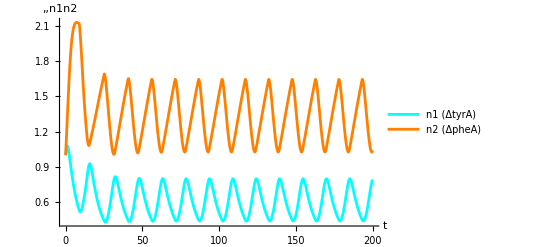

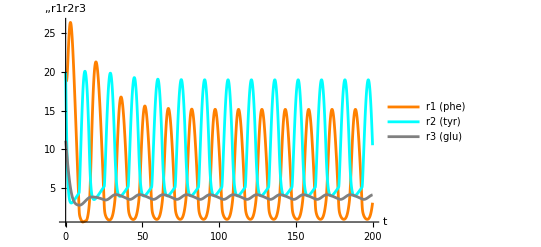

```mathematica
(* example simulation (limit cycle) *)
r1in=20;r2in=20;r3in=11.11;

sol=EcoSim[{n1->1,n2->1,r1->r1in,r2->r2in,r3->r3in},200];
PlotDynamics[sol,{n1,n2},PlotLegends->{"n1 (ΔtyrA)","n2 (ΔpheA)"}]
PlotDynamics[sol,{r1,r2,r3},PlotLegends->{"r1 (phe)","r2 (tyr)","r3 (glu)"}]
```

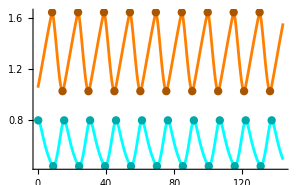

```mathematica
(* Supplementary Fig. 13a *)
sol2=EcoSim[Slice[sol,185],144];
Show[
PlotDynamics[sol2,{n1,n2},AxesLabel->None],
ListPlot[FindExtrema[n1/.sol2],PlotStyle->{PointSize[0.02],Darker@Color[n1]}],
ListPlot[FindExtrema[n2/.sol2],PlotStyle->{PointSize[0.02],Darker@Color[n2]}],
ImageSize->300
]
```

## SI3: Relating serial batch and continuous culture model dynamics

```mathematica
SetModel[{
Pop[n1]->{Equation:>μ1 n1,Color->Cyan}, (* ΔtyrA - needs r2 and r3, makes r1 *)
Pop[n2]->{Equation:>μ2 n2,Color->Orange}, (* ΔpheA - needs r1 and r3, makes r2 *)
Aux[r1]->{Equation:>n1 SuperPlus[(μ13-μ12)] q11-μ2 n2 q21,Color->Orange,Range->Interval[{0,∞}]}, (* phe *)
Aux[r2]->{Equation:>n2 SuperPlus[(μ23-μ21)] q22-μ1 n1 q12,Color->Cyan,Range->Interval[{0,∞}]}, (* tyr *)
Aux[r3]->{Equation:>-μ13 n1 q13-μ23 n2 q23,Color->Gray,Range->Interval[{0,∞}]},(* glu *)
WhenEvents->{WhenEvent[Mod[t,τ],{
n1[t]->n1[t]E^(-d τ),
n2[t]->n2[t]E^(-d τ),
r1[t]->r1[t]E^(-d τ)+r1in d τ,
r2[t]->r2[t]E^(-d τ)+r2in d τ,
r3[t]->r3[t]E^(-d τ)+r3in d τ
}]},
Parameters:>{μ1max>0,k12>0,k13>0,q11>0,q12>0,q13>0,μ2max>0,k21>0,k23>0,q21>0,q22>0,q23>0,d>0,r1in>=0,r2in>=0,r3in>=0,τ>=0}
}]
```

```mathematica
(* growth functions *)
μ13:=μ1max*r3/(k13+r3); μ12:=μ1max*r2/(k12+r2);
μ23:=μ2max*r3/(k23+r3); μ21:=μ2max*r1/(k21+r1);
μ1:=Min[μ13,μ12];
μ2:=Min[μ23,μ21];
```

```mathematica
(* inferred parameters (Supplementary Table 1) *)
μ1max=0.7045;μ2max=0.9517;
k13=3.7551;k23=10.698;
k12=20.867;k21=8.6907;
q13=1.277;q23=3.5704;
q12=43.302;q21=39.073;
q11=80.364;q22=46.602;
d=0.2;
r1in=20;r2in=20;r3in=11.11;
```

### Bifurcation diagram (Supplementary Fig. 12)

```mathematica
ϵ=10^-6;
```

```mathematica
(* generate data -- takes 20-25 minutes *)
Clear[τ]
Dynamic[τ]
res=Table[
ics={n1->0.05,n2->0.05,r1->r1in,r2->r2in,r3->r3in};
np=Round[2400/τ];
warmup=EcoSim[ics,np τ-ϵ,Output->"FinalSlice"];
np=Round[720/τ];
sol=EcoSim[warmup,np τ-ϵ];
pts1=n1/.Slice[sol,#]&/@Table[p τ-ϵ,{p,1,np-1}];
pts2=n2/.Slice[sol,#]&/@Table[p τ-ϵ,{p,1,np-1}];
{τ,
FinalSlice[sol],
DeleteDuplicates[pts1,Abs[#1-#2]<=0.001&],
Join[DeleteDuplicates[-Check[FindPeaks[-pts1][[2;;-2,2]],{}],Abs[#1-#2]<=0.001&],
DeleteDuplicates[Check[FindPeaks[pts1][[2;;-2,2]],{}],Abs[#1-#2]<=0.001&]],
DeleteDuplicates[pts2,Abs[#1-#2]<=0.001&],
Join[DeleteDuplicates[-Check[FindPeaks[-pts2][[2;;-2,2]],{}],Abs[#1-#2]<=0.001&],
DeleteDuplicates[Check[FindPeaks[pts2][[2;;-2,2]],{}],Abs[#1-#2]<=0.001&]]
}
,{τ,0.005,30,0.005}];
```

```mathematica
bif1=Show[
ListPlot[MakeXY[res[[All,{1,3}]]],PlotStyle->{PointSize[0.001],Color[n1]}],
ListPlot[MakeXY[res[[All,{1,4}]]],PlotStyle->{PointSize[0.002],Darker@Color[n1]}],
ListPlot[MakeXY[res[[All,{1,5}]]],PlotStyle->{PointSize[0.001],Color[n2]}],
ListPlot[MakeXY[res[[All,{1,6}]]],PlotStyle->{PointSize[0.002],Darker@Color[n2]}],
ImageSize->800,AspectRatio->0.4,PlotRange->{All,{0,All}},Frame->{True,True,False,False},FrameTicks->All,FrameTicksStyle->16
]
```

-Graphics-

```mathematica
bif2=Show[
ListPlot[MakeXY[res[[1;;6*200,{1,3}]]],PlotStyle->{PointSize[0.001],Color[n1]}],
ListPlot[MakeXY[res[[1;;6*200,{1,4}]]],PlotStyle->{PointSize[0.002],Darker@Color[n1]}],
ListPlot[MakeXY[res[[1;;6*200,{1,5}]]],PlotStyle->{PointSize[0.001],Color[n2]}],
ListPlot[MakeXY[res[[1;;6*200,{1,6}]]],PlotStyle->{PointSize[0.002],Darker@Color[n2]}],
ImageSize->800,AspectRatio->0.4,PlotRange->{All,{0,All}},Frame->{True,True,False,False},FrameTicks->All,FrameTicksStyle->16
]
```

-Graphics-

### Plot dynamics (Supplementary Fig. 13)

```mathematica
tmax=144;
```

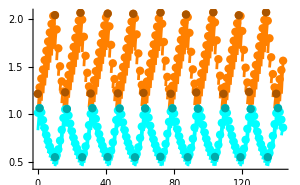

```mathematica
(* b) aperiodic *)
τ=1.0;
ics=res[[Round[τ/0.005],2]];
np=Floor[tmax/τ];
sol=EcoSim[EcoSim[ics,6τ-ϵ,Output->"FinalSlice"],np τ];
pts1=Table[{i τ,n1/.Slice[sol,i τ]},{i,0,np}];
pts2=Table[{i τ,n2/.Slice[sol,i τ]},{i,0,np}];
Show[
PlotDynamics[sol,{n1,n2},AxesLabel->None,Exclusions->Table[i τ,{i,np}]],
ListPlot[pts1,PlotStyle->{PointSize[0.02],Color[n1]}],
ListPlot[FindExtrema[pts1][[2;;-2]],PlotStyle->{PointSize[0.02],Darker@Color[n1]}],
ListPlot[pts2,PlotStyle->{PointSize[0.02],Color[n2]}],
ListPlot[FindExtrema[pts2][[1;;-2]],PlotStyle->{PointSize[0.02],Darker@Color[n2]}],
ImageSize->300
]
```

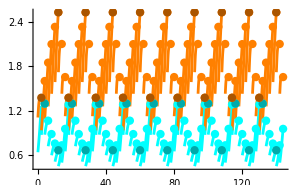

```mathematica
(* c) 8-cycle *)
τ=2.0;
ics=res[[Round[τ/0.005],2]];
np=Floor[tmax/τ];
sol=EcoSim[EcoSim[ics,5τ-ϵ,Output->"FinalSlice"],np τ];
pts1=Table[{i τ,n1/.Slice[sol,i τ-ϵ]},{i,1,np}];
pts2=Table[{i τ,n2/.Slice[sol,i τ-ϵ]},{i,1,np}];
Show[
PlotDynamics[sol,{n1,n2},AxesLabel->None,Exclusions->Table[i τ,{i,np}]],
ListPlot[pts1[[2;;]],PlotStyle->{PointSize[0.02],Color[n1]}],
ListPlot[FindExtrema[pts1[[;;-3]]],PlotStyle->{PointSize[0.02],Darker@Color[n1]}],
ListPlot[pts2[[2;;]],PlotStyle->{PointSize[0.02],Color[n2]}],
ListPlot[FindExtrema[pts2[[;;-3]]],PlotStyle->{PointSize[0.02],Darker@Color[n2]}],
ImageSize->300
]
```

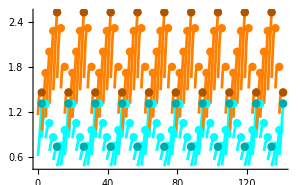

```mathematica
(* d) 7-cycle *)
τ=2.2;
ics=res[[Round[τ/0.005],2]];
np=Floor[tmax/τ]-1;
sol=EcoSim[EcoSim[ics,2τ-ϵ,Output->"FinalSlice"],np τ];
pts1=Table[{i τ,n1/.Slice[sol,i τ-ϵ]},{i,1,np}];
pts2=Table[{i τ,n2/.Slice[sol,i τ-ϵ]},{i,1,np}];
Show[
PlotDynamics[sol,{n1,n2},AxesLabel->None,Exclusions->Table[i τ,{i,np}]],
ListPlot[pts1[[2;;]],PlotStyle->{PointSize[0.02],Color[n1]}],
ListPlot[FindExtrema[pts1],PlotStyle->{PointSize[0.02],Darker@Color[n1]}],
ListPlot[pts2[[2;;]],PlotStyle->{PointSize[0.02],Color[n2]}],
ListPlot[FindExtrema[pts2],PlotStyle->{PointSize[0.02],Darker@Color[n2]}],
ImageSize->300
]
```

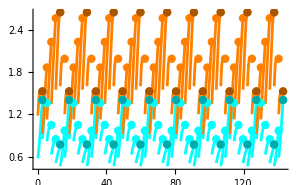

```mathematica
(* e) 6-cycle *)
τ=2.6;
ics=res[[Round[τ/0.005],2]];
np=Floor[tmax/τ];
sol=EcoSim[EcoSim[ics,5τ-ϵ,Output->"FinalSlice"],np τ];
pts1=Table[{i τ,n1/.Slice[sol,i τ-ϵ]},{i,1,np}];
pts2=Table[{i τ,n2/.Slice[sol,i τ-ϵ]},{i,1,np}];
Show[
PlotDynamics[sol,{n1,n2},AxesLabel->None,Exclusions->Table[i τ,{i,np}]],
ListPlot[pts1,PlotStyle->{PointSize[0.02],Color[n1]}],
ListPlot[FindExtrema[pts1],PlotStyle->{PointSize[0.02],Darker@Color[n1]}],
ListPlot[pts2,PlotStyle->{PointSize[0.02],Color[n2]}],
ListPlot[FindExtrema[pts2],PlotStyle->{PointSize[0.02],Darker@Color[n2]}],
ImageSize->300
]
```

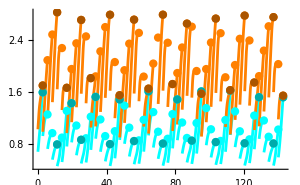

```mathematica
(* f) aperiodic *)
τ=2.8;
ics=res[[Round[τ/0.005],2]];
np=Floor[tmax/τ];
sol=EcoSim[EcoSim[ics,5τ-ϵ,Output->"FinalSlice"],np τ];
pts1=Table[{i τ,n1/.Slice[sol,i τ-ϵ]},{i,1,np}];
pts2=Table[{i τ,n2/.Slice[sol,i τ-ϵ]},{i,1,np}];
Show[
PlotDynamics[sol,{n1,n2},AxesLabel->None,Exclusions->Table[i τ,{i,np}]],
ListPlot[pts1,PlotStyle->{PointSize[0.02],Color[n1]}],
ListPlot[FindExtrema[pts1],PlotStyle->{PointSize[0.02],Darker@Color[n1]}],
ListPlot[pts2,PlotStyle->{PointSize[0.02],Color[n2]}],
ListPlot[FindExtrema[pts2],PlotStyle->{PointSize[0.02],Darker@Color[n2]}],
ImageSize->300
]
```

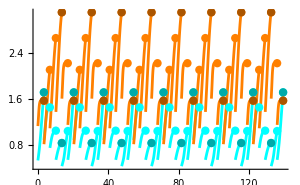

```mathematica
(* g) 5-cycle *)
τ=3.4;
ics=res[[Round[τ/0.005],2]];
np=Floor[tmax/τ]-1;
sol=EcoSim[EcoSim[ics,3τ-ϵ,Output->"FinalSlice"],np τ];
pts1=Table[{i τ,n1/.Slice[sol,i τ-ϵ]},{i,1,np}];
pts2=Table[{i τ,n2/.Slice[sol,i τ-ϵ]},{i,1,np}];
Show[
PlotDynamics[sol,{n1,n2},AxesLabel->None,Exclusions->Table[i τ,{i,np}]],
ListPlot[pts1,PlotStyle->{PointSize[0.02],Color[n1]}],
ListPlot[FindExtrema[pts1],PlotStyle->{PointSize[0.02],Darker@Color[n1]}],
ListPlot[pts2,PlotStyle->{PointSize[0.02],Color[n2]}],
ListPlot[FindExtrema[pts2],PlotStyle->{PointSize[0.02],Darker@Color[n2]}],
ImageSize->300
]
```

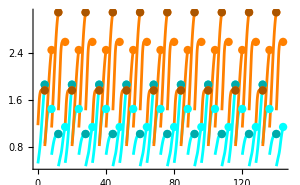

```mathematica
(* h) 4-cycle *)
τ=4.0;
ics=res[[Round[τ/0.005],2]];
np=Floor[tmax/τ];
sol=EcoSim[EcoSim[ics,3τ-ϵ,Output->"FinalSlice"],np τ];
pts1=Table[{i τ,n1/.Slice[sol,i τ-ϵ]},{i,1,np}];
pts2=Table[{i τ,n2/.Slice[sol,i τ-ϵ]},{i,1,np}];
Show[
PlotDynamics[sol,{n1,n2},AxesLabel->None,Exclusions->Table[i τ,{i,np}]],
ListPlot[pts1,PlotStyle->{PointSize[0.02],Color[n1]}],
ListPlot[FindExtrema[pts1[[;;-2]]],PlotStyle->{PointSize[0.02],Darker@Color[n1]}],
ListPlot[pts2,PlotStyle->{PointSize[0.02],Color[n2]}],
ListPlot[FindExtrema[pts2[[;;-2]]],PlotStyle->{PointSize[0.02],Darker@Color[n2]}],
ImageSize->300
]
```

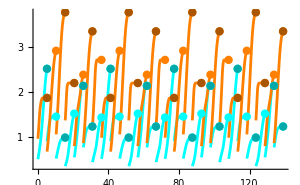

```mathematica
(* i) 7-cycle *)
τ=5.15;
ics=res[[Round[τ/0.005],2]];
np=Floor[tmax/τ];
sol=EcoSim[EcoSim[ics,4τ-ϵ,Output->"FinalSlice"],np τ];
pts1=Table[{i τ,n1/.Slice[sol,i τ-ϵ]},{i,1,np}];
pts2=Table[{i τ,n2/.Slice[sol,i τ-ϵ]},{i,1,np}];
Show[
PlotDynamics[sol,{n1,n2},AxesLabel->None,Exclusions->Table[i τ,{i,np}]],
ListPlot[pts1,PlotStyle->{PointSize[0.02],Color[n1]}],
ListPlot[FindExtrema[pts1],PlotStyle->{PointSize[0.02],Darker@Color[n1]}],
ListPlot[pts2,PlotStyle->{PointSize[0.02],Color[n2]}],
ListPlot[FindExtrema[pts2],PlotStyle->{PointSize[0.02],Darker@Color[n2]}],
ImageSize->300
]
```

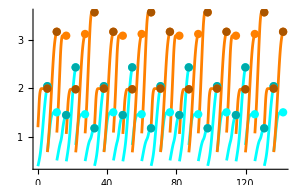

```mathematica
(* j) 6-cycle (period-doubled 3-cycle) *)
τ=5.45;
ics=res[[Round[τ/0.005],2]];
np=Floor[tmax/τ];
sol=EcoSim[EcoSim[ics,3τ-ϵ,Output->"FinalSlice"],np τ];
pts1=Table[{i τ,n1/.Slice[sol,i τ-ϵ]},{i,1,np}];
pts2=Table[{i τ,n2/.Slice[sol,i τ-ϵ]},{i,1,np}];
Show[
PlotDynamics[sol,{n1,n2},AxesLabel->None,Exclusions->Table[i τ,{i,np}]],
ListPlot[pts1,PlotStyle->{PointSize[0.02],Color[n1]}],
ListPlot[FindExtrema[pts1[[;;-2]]],PlotStyle->{PointSize[0.02],Darker@Color[n1]}],
ListPlot[pts2,PlotStyle->{PointSize[0.02],Color[n2]}],
ListPlot[FindExtrema[pts2],PlotStyle->{PointSize[0.02],Darker@Color[n2]}],
ImageSize->300
]
```

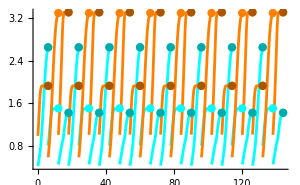

```mathematica
(* k) 3-cycle *)
τ=6.0;
ics=res[[Round[τ/0.005],2]];
np=Floor[tmax/τ];
sol=EcoSim[EcoSim[ics,τ-ϵ,Output->"FinalSlice"],np τ];
pts1=Table[{i τ,n1/.Slice[sol,i τ-ϵ]},{i,1,np}];
pts2=Table[{i τ,n2/.Slice[sol,i τ-ϵ]},{i,1,np}];
Show[
PlotDynamics[sol,{n1,n2},AxesLabel->None,Exclusions->Table[i τ,{i,np}]],
ListPlot[pts1,PlotStyle->{PointSize[0.02],Color[n1]}],
ListPlot[FindExtrema[pts1],PlotStyle->{PointSize[0.02],Darker@Color[n1]}],
ListPlot[pts2,PlotStyle->{PointSize[0.02],Color[n2]}],
ListPlot[FindExtrema[pts2],PlotStyle->{PointSize[0.02],Darker@Color[n2]}],
ImageSize->300
]
```

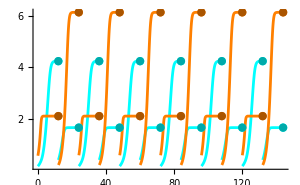

```mathematica
(* l) 2-cycle *)
τ=12.0;
ics=res[[Round[τ/0.005],2]];
np=Floor[tmax/τ];
sol=EcoSim[EcoSim[ics,τ-ϵ,Output->"FinalSlice"],np τ];
pts1=Table[{i τ,n1/.Slice[sol,i τ-ϵ]},{i,1,np}];
pts2=Table[{i τ,n2/.Slice[sol,i τ-ϵ]},{i,1,np}];
Show[
PlotDynamics[sol,{n1,n2},AxesLabel->None,Exclusions->Table[i τ,{i,np}]],
ListPlot[pts1,PlotStyle->{PointSize[0.02],Color[n1]}],
ListPlot[FindExtrema[pts1],PlotStyle->{PointSize[0.02],Darker@Color[n1]}],
ListPlot[pts2,PlotStyle->{PointSize[0.02],Color[n2]}],
ListPlot[FindExtrema[pts2],PlotStyle->{PointSize[0.02],Darker@Color[n2]}],
ImageSize->300
]
```

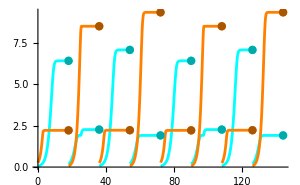

```mathematica
(* m) 4-cycle (period-doubled 2-cycle) *)
τ=18.0;
ics=res[[Round[τ/0.005],2]];
np=Floor[tmax/τ];
sol=EcoSim[EcoSim[ics,τ-ϵ,Output->"FinalSlice"],np τ];
pts1=Table[{i τ,n1/.Slice[sol,i τ-ϵ]},{i,1,np}];
pts2=Table[{i τ,n2/.Slice[sol,i τ-ϵ]},{i,1,np}];
Show[
PlotDynamics[sol,{n1,n2},AxesLabel->None,Exclusions->Table[i τ,{i,np}]],
ListPlot[pts1,PlotStyle->{PointSize[0.02],Color[n1]}],
ListPlot[FindExtrema[pts1],PlotStyle->{PointSize[0.02],Darker@Color[n1]}],
ListPlot[pts2,PlotStyle->{PointSize[0.02],Color[n2]}],
ListPlot[FindExtrema[pts2],PlotStyle->{PointSize[0.02],Darker@Color[n2]}],
ImageSize->300
]
```

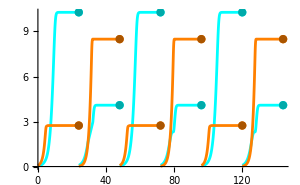

```mathematica
(* n) 2-cycle *)
τ=24.0;
ics=res[[Round[τ/0.005],2]];
np=Floor[tmax/τ];
sol=EcoSim[ics,np τ];
pts1=Table[{i τ,n1/.Slice[sol,i τ-ϵ]},{i,1,np}];
pts2=Table[{i τ,n2/.Slice[sol,i τ-ϵ]},{i,1,np}];
Show[
PlotDynamics[sol,{n1,n2},AxesLabel->None,Exclusions->Table[i τ,{i,np}]],
ListPlot[pts1,PlotStyle->{PointSize[0.02],Color[n1]}],
ListPlot[FindExtrema[pts1],PlotStyle->{PointSize[0.02],Darker@Color[n1]}],
ListPlot[pts2,PlotStyle->{PointSize[0.02],Color[n2]}],
ListPlot[FindExtrema[pts2],PlotStyle->{PointSize[0.02],Darker@Color[n2]}],
ImageSize->300
]
```

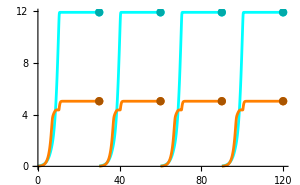

```mathematica
(* o) 1-cycle *)
τ=30.0;
ics=res[[Round[τ/0.005],2]];
np=Floor[tmax/τ];
sol=EcoSim[ics,np τ];
pts1=Table[{i τ,n1/.Slice[sol,i τ-ϵ]},{i,1,np}];
pts2=Table[{i τ,n2/.Slice[sol,i τ-ϵ]},{i,1,np}];
Show[
PlotDynamics[sol,{n1,n2},AxesLabel->None,Exclusions->Table[i τ,{i,np}]],
ListPlot[pts1,PlotStyle->{PointSize[0.02],Color[n1]}],
ListPlot[FindExtrema[pts1],PlotStyle->{PointSize[0.02],Darker@Color[n1]}],
ListPlot[pts2,PlotStyle->{PointSize[0.02],Color[n2]}],
ListPlot[FindExtrema[pts2],PlotStyle->{PointSize[0.02],Darker@Color[n2]}],
ImageSize->300
]
```

## SI4: Deriving a minimal model for analysis of the resource dynamics

```mathematica
Clear["Global`*"]
$Assumptions={q11>0,q12>0,q21>0,q22>0,r3>0,1>f>0,d>0,ntot>0,a12>0,a21>0,a13>0,a23>0};
```

### R1-R2 subsystem (Eqn S2)

```mathematica
dr1:=-d r1+q11(a13 r3-Min[a12 r2,a13 r3])f ntot-q21 Min[a21 r1,a23 r3](1-f)ntot;
dr2:=-d r2+q22(a23 r3-Min[a21 r1,a23 r3])(1-f)ntot-q12 Min[a12 r2,a13 r3]f ntot;
df:=(Min[a12 r2,a13 r3]-Min[a21 r1,a23 r3])f(1-f);
```

#### Four equilibria

```mathematica
(* Equilibrium 1: R3-limited N1 (consumer), R1-limited N2 (producer) (Eqns S3-4) *)
lim={Min[a12 r2,a13 r3]->a13 r3,Min[a21 r1,a23 r3]->a21 r1};
eqns1={0==dr1,0==dr2}/.lim;
eq1=Simplify@Solve[eqns1,{r1,r2}][[1]]
```

{r1→0,r2→-(ntot (a13 f q12+a23 (-1+f) q22) r3)/d}

```mathematica
(* Equilibrium 2: R3-limited N2 (consumer), R2-limited N1 (producer) (Eqns S5-6) *)
lim={Min[a12 r2,a13 r3]->a12 r2,Min[a21 r1,a23 r3]->a23 r3};
eqns2={0==dr1,0==dr2}/.lim;
eq2=Simplify@Solve[eqns2,{r1,r2}][[1]]
```

{r1→(ntot (a13 f q11+a23 (-1+f) q21) r3)/d,r2→0}

```mathematica
(* Equilibrium 3: both amino acid limited (Eqn S7) *)
lim={Min[a12 r2,a13 r3]->a12 r2,Min[a21 r1,a23 r3]->a21 r1};
eqns3={0==dr1,0==dr2}/.lim;
eq3=FullSimplify@Solve[eqns3,{r1,r2}][[1]]
```

{r1→(f ntot q11 (a13 (d+a12 f ntot q12)+a12 a23 (-1+f) ntot q22) r3)/((d+a12 f ntot q12) (d-a21 (-1+f) ntot q21)+a12 a21 (-1+f) f ntot^2 q11 q22),r2→((-1+f) ntot (-a23 d+a13 a21 f ntot q11+a21 a23 (-1+f) ntot q21) q22 r3)/((d+a12 f ntot q12) (d-a21 (-1+f) ntot q21)+a12 a21 (-1+f) f ntot^2 q11 q22)}

```mathematica
(* Equilibrium 4: both glucose limited => both resouces negative = inconsistent (Eqn S8) *)
lim={Min[a12 r2,a13 r3]->a13 r3,Min[a21 r1,a23 r3]->a23 r3};
eqns4={0==dr1,0==dr2}/.lim;
eq4=Solve[eqns4,{r1,r2}][[1]]
```

{r1→(a23 (-1+f) ntot q21 r3)/d,r2→-(a13 f ntot q12 r3)/d}

#### Deriving the critical f (Eqns. S4&6) four different ways

```mathematica
(* ri from eq3 equals zero *)
Solve[(r1/.eq3)==0,f]
Solve[(r2/.eq3)==0,f]
```

{{f→0},{f→(-a13 d+a12 a23 ntot q22)/(a12 ntot (a13 q12+a23 q22))}}

{{f→1},{f→(a23 d+a21 a23 ntot q21)/(a21 ntot (a13 q11+a23 q21))}}

```mathematica
(* colimitation of boundary equilibria eq1 & eq2 *)
Solve[(a12 r2==a13 r3)/.eq1,f]
Solve[(a21 r1==a23 r3)/.eq2,f]
```

{{f→(-a13 d+a12 a23 ntot q22)/(a12 ntot (a13 q12+a23 q22))}}

{{f→(a23 d+a21 a23 ntot q21)/(a21 ntot (a13 q11+a23 q21))}}

```mathematica
(* colimitation of central equilibrium eq3 *)
Solve[(a12 r2==a13 r3)/.eq3,f]
Solve[(a21 r1==a23 r3)/.eq3,f]
```

{{f→(d+a21 ntot q21)/(a21 ntot q21)},{f→(-a13 d+a12 a23 ntot q22)/(a12 ntot (a13 q12+a23 q22))}}

{{f→-d/(a12 ntot q12)},{f→(a23 d+a21 a23 ntot q21)/(a21 ntot (a13 q11+a23 q21))}}

```mathematica
(* eq3 meets eq1 & eq2 *)
Simplify@Solve[(r1/.eq2)==(r1/.eq3),f]
Simplify@Solve[(r2/.eq1)==(r2/.eq3),f]
```

{{f→1},{f→(a23 d+a21 a23 ntot q21)/(a13 a21 ntot q11+a21 a23 ntot q21)},{f→(d q21)/(-a12 ntot q12 q21+a12 ntot q11 q22)}}

{{f→0},{f→-(a13 d-a12 a23 ntot q22)/(a12 a13 ntot q12+a12 a23 ntot q22)},{f→(d q12+a21 ntot q12 q21-a21 ntot q11 q22)/(a21 ntot q12 q21-a21 ntot q11 q22)}}

All the same!

```mathematica
fc1:=(-a13 d+a12 a23 ntot q22)/(a12 ntot (a13 q12+a23 q22));
fc2:=(a23 d+a21 a23 ntot q21)/(a21 ntot (a13 q11+a23 q21));
```

Critical d where fc1=fc2:

```mathematica
Simplify@Solve[fc1==fc2,d][[1]]
```

{d→(a12 a13 a21 a23 ntot (-q12 q21+q11 q22))/(a13^2 a21 q11+a13 a23 (a12 q12+a21 q21)+a12 a23^2 q22)}

#### Stability analysis

```mathematica
(* eq1 *)
j1:=D[eqns1/.RHS,{{r1,r2}}];
j1//MatrixForm
```

(-d-a21 (1-f) ntot q21 | 0
-a21 (1-f) ntot q22 | -d)

```mathematica
Eigenvalues[j1]
```

{-d,-d-a21 ntot q21+a21 f ntot q21}

```mathematica
Simplify[-d-a21 ntot q21+a21 f ntot q21<0]
```

True

Since both eigenvalues are negative, eq1 is stable.

```mathematica
(* eq2 *)
j2:=D[eqns2/.RHS,{{r1,r2}}];
j2//MatrixForm
```

(-d | -a12 f ntot q11
0 | -d-a12 f ntot q12)

```mathematica
Eigenvalues[j2]
```

{-d,-d-a12 f ntot q12}

```mathematica
Simplify[-d-a12 f ntot q12<0]
```

True

Since both eigenvalues are negative, eq2 is stable.

```mathematica
(* eq3 *)
j3:=D[eqns3/.RHS,{{r1,r2}}];
j3//MatrixForm
```

(-d-a21 (1-f) ntot q21 | -a12 f ntot q11
-a21 (1-f) ntot q22 | -d-a12 f ntot q12)

We can show stability depending on ordering of fcrit’s using Routh-Hurwitz criteria, Det[j3]>0 and Tr[j3]<0:

```mathematica
(* trace is always negative (stable) *)
Tr[j3/.eq3]
Simplify[Tr[j3/.eq3]<0]
```

-2 d-a12 f ntot q12-a21 (1-f) ntot q21

True

```mathematica
(* determinant is more tricky *)
FullSimplify[Det[j3/.eq3]>0]
```

(d+a12 f ntot q12) (d-a21 (-1+f) ntot q21)+a12 a21 (-1+f) f ntot^2 q11 q22>0

```mathematica
(* here's a simpler, necessary condition *)
FullSimplify[(Det[j3/.eq3]/.d->0)>0]
```

q11 q22<q12 q21

```mathematica
(* increasing d is stabilizing *)
FullSimplify[D[Simplify[Det[j3/.eq3]],d]>0]
```

True

```mathematica
FullSimplify[fc1<fc2]
```

a13 d (a13 a21 q11+a12 a23 q12)+a13 a21 a23 (d+a12 ntot q12) q21+a12 a23 (a23 d-a13 a21 ntot q11) q22>0

```mathematica
FullSimplify[Det[j3/.eq3/.f->fc1]>0]
```

a13 d (a13 a21 q11+a12 a23 q12)+a13 a21 a23 (d+a12 ntot q12) q21+a12 a23 (a23 d-a13 a21 ntot q11) q22>0

```mathematica
FullSimplify[Det[j3/.eq3/.f->fc2]>0]
```

a13 d (a13 a21 q11+a12 a23 q12)+a13 a21 a23 (d+a12 ntot q12) q21+a12 a23 (a23 d-a13 a21 ntot q11) q22>0

```mathematica
FullSimplify[(fc1<fc2)==(Det[j3/.eq3/.f->fc1]>0)]
FullSimplify[(fc1<fc2)==(Det[j3/.eq3/.f->fc2]>0)]
```

True

True

```mathematica
FullSimplify[D[Simplify[Det[j3/.eq3]],f]]
```

-ntot (-a12 d q12+a21 d q21+a12 a21 (-1+2 f) ntot (q12 q21-q11 q22))

```mathematica
(* show that increasing d stabilizes eq3 (Eqn. S9) *)
FullSimplify[D[Simplify[Det[j3/.eq3]],d]>0]
```

True

#### Examples (Supplementary Fig. 9)

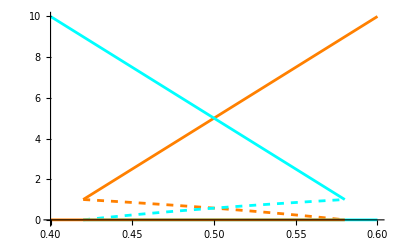

```mathematica
(* r1-r2 subsystem bifurcation diagram *)
Clear[f];
ntot=1;
r3=1;
q11=1.5;
q12=1;
q21=1;
q22=1.5;
d=0.05;
a13=a23=a12=a21=1;

Show[
Plot[Evaluate[{r1,r2}/.eq3],{f,fc1,fc2},PlotStyle->{{Orange,Dashed},{Cyan,Dashed}},PlotRange->{{0.4,0.6},{-0.1,10}}],
Plot[Evaluate[{r1,r2}/.eq2],{f,fc2,0.6},PlotStyle->{Orange,Cyan}],
Plot[Evaluate[{r1,r2}/.eq1],{f,0.4,fc1},PlotStyle->{Orange,Cyan}]
]
```

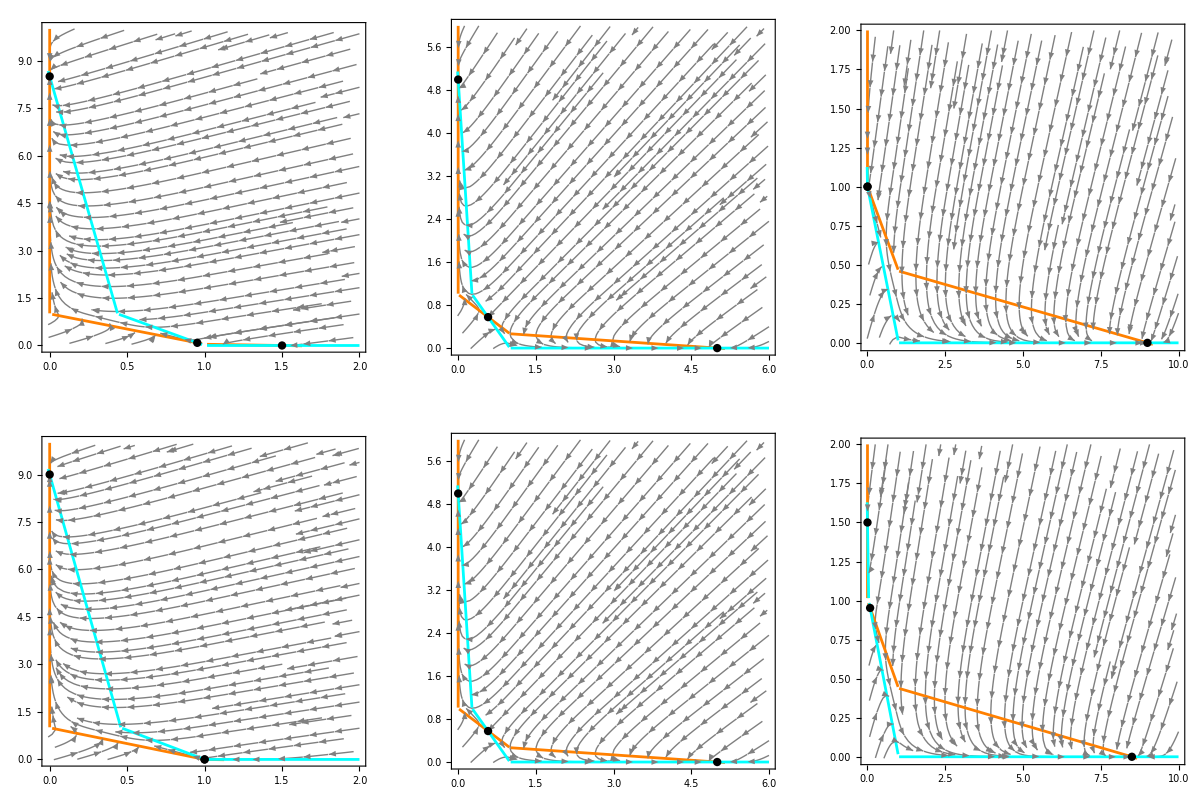

```mathematica
(* phase planes *)
rmin=-0.01;
phaseplane[fin_,r1max_,r2max_]:=Block[{f=fin},
Show[
MyStreamPlot[{dr1,dr2},{r1,rmin,r1max},{r2,rmin,r2max},StreamStyle->Gray,StreamColorFunction->None],
ContourPlot[0==dr1,{r1,rmin,r1max},{r2,rmin,r2max},ContourShading->None,ContourStyle->Orange,PlotPoints->200,PlotRange->{{0,r1max},{0,r2max}}],
ContourPlot[0==dr2,{r1,rmin,r1max},{r2,rmin,r2max},ContourShading->None,ContourStyle->Cyan,PlotPoints->200],
ListPlot[{r1,r2}/.{eq3,eq2,eq1}/.f->fin,PlotRange->{{0,r1max},{0,r2max}},PlotStyle->{{Black,PointSize[0.02]}}],
ImageSize->300
]];

GraphicsGrid[{{phaseplane[0.43,2,10],phaseplane[0.5,6,6],phaseplane[0.58,10,2]},
{phaseplane[0.42,2,10],phaseplane[0.5,6,6],phaseplane[0.57,10,2]}}]
```